# Practica 2: Sistemas de ecuaciones diferenciales, alumnos

## Sistemas de ecuaciones diferenciales

### Sistemas de ecuaciones diferenciales no homogéneos con coeficientes constantes

De cada uno de los siguientes sistemas de ecuaciones diferenciales obtenga:

a) Los valores de estado estacionario.
b) El análisis de estabilidad.
c) El diagrama de fases.

1.	ẋ=-3x+y+3
	ẏ=  x-3y+3

a) Valores de estado estacionario

```mathematica
<<VectorFieldPlots`
```

General::obspkg: "VectorFieldPlots`" is now obsolete. The legacy version being loaded may conflict with current Mathematica functionality. See the Compatibility Guide for updating information.

```mathematica
A1={{-3,1},{1,-3}};MatrixForm[A1](* Matriz A de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(-3 | 1
1 | -3)

```mathematica
b1={{3},{3}};MatrixForm[b1](* Vector b de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(3
3)

```mathematica
MatrixForm[LinearSolve[-A1,b1]](* Esto equivale a ({{Subscript[x, 1]^-}, {(x^-)_2}})=-A^-1b *)
```

(3/2
3/2)

b) Análisis de estabilidad

```mathematica
traA1=Tr[A1](*Traza de la matriz A*)
```

-6

```mathematica
detA1=Det[A1](*Determinante de la matriz A*)
```

8

```mathematica
(traA1)^2-4detA1(* (TrazaA)^2-4det|A| *)
```

4

```mathematica
ec1=CharacteristicPolynomial[A1,λ] (* Polinomio caracteristico de la matriz A *)
```

8+6 λ+λ^2

```mathematica
Solve[ec1==0,λ](* Obteniendo los valores propios *)
```

{{λ→-4},{λ→-2}}

c) Diagrama de fases

```mathematica
eq1={x'[t]==-3x[t]+y[t]+3,y'[t]==x[t]-3y[t]+3};
```

```mathematica
var1={x[t],y[t]};
```

```mathematica
sol1=DSolve[eq1,var1,t];
```

```mathematica
p1=ContourPlot[{-3x+y+3==0,x-3y+3==0},{x,0,3},{y,0,3},Axes->True,Frame->False];
```

```mathematica
p2=VectorFieldPlot[{-3x+y+3,x-3y+3},{x,0,3},{y,0,3},ScaleFunction->(1 &),AspectRatio->1];
```

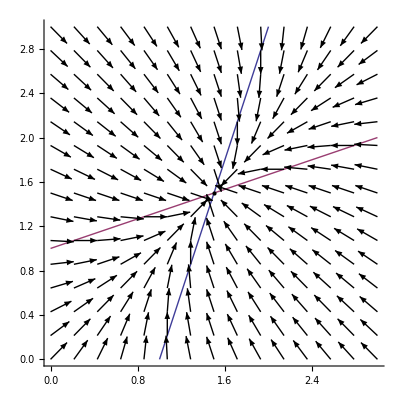

```mathematica
Show[p1,p2]
```

```mathematica
Clear[A1,b1,ec1,eq1,var1,sol1,p1,p2]
```

2.	ẋ=    x+  y-4
	ẏ=-2x+4y-4

a) Valores de estado estacionario

```mathematica
A2={{1,1},{-2,4}};MatrixForm[A2](* Matriz A de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(1 | 1
-2 | 4)

```mathematica
b2={{-4},{-4}};MatrixForm[b2](* Vector b de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(-4
-4)

```mathematica
MatrixForm[LinearSolve[-A2,b2]](* Esto equivale a ({{Subscript[x, 1]^-}, {(x^-)_2}})=-A^-1b *)
```

(2
2)

b) Análisis de estabilidad

```mathematica
traA2=Tr[A2](*Traza de la matriz A*)
```

5

```mathematica
detA2=Det[A2](*Determinante de la matriz A*)
```

6

```mathematica
(traA2)^2-4detA2(* (TrazaA)^2-4det|A| *)
```

1

```mathematica
ec2=CharacteristicPolynomial[A2,λ] (* Polinomio caracteristico de la matriz A *)
```

6-5 λ+λ^2

```mathematica
Solve[ec2==0,λ](* Obteniendo los valores propios *)
```

{{λ→2},{λ→3}}

c) Diagrama de fases

```mathematica
eq2={x'[t]==x[t]+y[t]-4,y'[t]==-2x[t]+4y[t]-4};
```

```mathematica
var2={x[t],y[t]};
```

```mathematica
sol2=DSolve[eq2,var2,t];
```

```mathematica
p3=ContourPlot[{x+y-4==0,-2x+4y-4==0},{x,0,4},{y,0,4},Axes->True,Frame->False];
```

```mathematica
p4=VectorFieldPlot[{x+y-4,-2x+4y-4},{x,0,4},{y,0,4},ScaleFunction->(1 &),AspectRatio->1];
```

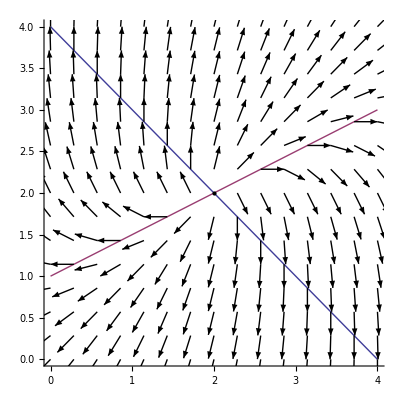

```mathematica
Show[p3,p4]
```

```mathematica
Clear[A2,b2,ec2,eq2,var2,sol2,p3,p4]
```

3.	ẋ=  x+12y-25
	ẏ=3x+   y-5

a) Valores de estado estacionario

```mathematica
A3={{1,12},{3,1}};MatrixForm[A3](* Matriz A de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(1 | 12
3 | 1)

```mathematica
b3={{-25},{-5}};MatrixForm[b3](* Vector b de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(-25
-5)

```mathematica
MatrixForm[LinearSolve[-A3,b3]](* Esto equivale a ({{Subscript[x, 1]^-}, {(x^-)_2}})=-A^-1b *)
```

(1
2)

b) Análisis de estabilidad

```mathematica
traA3=Tr[A3](*Traza de la matriz A*)
```

2

```mathematica
detA3=Det[A3](*Determinante de la matriz A*)
```

-35

```mathematica
(traA3)^2-4detA3(* (TrazaA)^2-4det|A| *)
```

144

```mathematica
ec3=CharacteristicPolynomial[A3,λ] (* Polinomio caracteristico de la matriz A *)
```

-35-2 λ+λ^2

```mathematica
Solve[ec3==0,λ](* Obteniendo los valores propios *)
```

{{λ→-5},{λ→7}}

c) Diagrama de fases

```mathematica
eq3={x'[t]==x[t]+12y[t]-25,y'[t]==3x[t]+y[t]-5};
```

```mathematica
var3={x[t],y[t]};
```

```mathematica
sol3=DSolve[eq3,var3,t];
```

```mathematica
p5=ContourPlot[{x+12y-25==0,3x+y-5==0},{x,0,2},{y,1,3},Axes->True,Frame->False];
```

```mathematica
p6=VectorFieldPlot[{x+12y-25,3x+y-5},{x,0,2},{y,1,3},ScaleFunction->(1 &),AspectRatio->1];
```

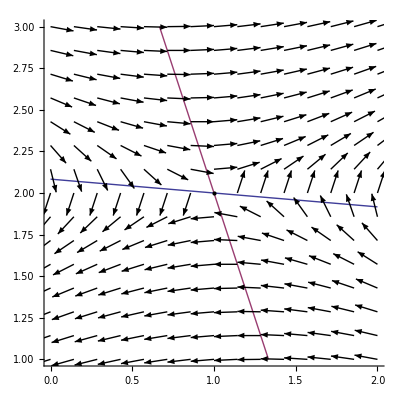

```mathematica
Show[p5,p6]
```

```mathematica
Clear[A3,b3,ec3,eq3,var3,sol3,p5,p6]
```

4.	ẋ=-3x+4y-4	c.i. 	x(0)=2
	ẏ=-2x+  y+9		y(0)=3

```mathematica
A4={{-3,4},{-2,1}};MatrixForm[A4](* Matriz A de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(-3 | 4
-2 | 1)

```mathematica
b4={{-4},{9}};MatrixForm[b4](* Vector b de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(-4
9)

```mathematica
MatrixForm[LinearSolve[-A4,b4]](* Esto equivale a ({{Subscript[x, 1]^-}, {(x^-)_2}})=-A^-1b *)
```

(8
7)

b) Análisis de estabilidad

```mathematica
traA4=Tr[A4](*Traza de la matriz A*)
```

-2

```mathematica
detA4=Det[A4](*Determinante de la matriz A*)
```

5

```mathematica
(traA4)^2-4detA4(* (TrazaA)^2-4det|A| *)
```

-16

```mathematica
ec4=CharacteristicPolynomial[A4,λ] (* Polinomio caracteristico de la matriz A *)
```

5+2 λ+λ^2

```mathematica
Solve[ec4==0,λ](* Obteniendo los valores propios *)
```

{{λ→-1-2 ⅈ},{λ→-1+2 ⅈ}}

c) Diagrama de fases

```mathematica
eq4={x'[t]==-3x[t]+4y[t]-4,y'[t]==-2x[t]+y[t]+9,x[0]==2,y[0]==3};
```

```mathematica
var4={x[t],y[t]};
```

```mathematica
sol4=DSolve[eq4,var4,t];
```

```mathematica
p7=ContourPlot[{-3x+4y-4==0,-2x+y+9==0},{x,0,12},{y,2,10},Axes->True,Frame->False];
```

```mathematica
p8=VectorFieldPlot[{-3x+4y-4,-2x+y+9},{x,0,12},{y,2,10},ScaleFunction->(1 &),AspectRatio->1];
```

```mathematica
p9=ParametricPlot[Evaluate[var4/.sol4],{t,0,7},PlotStyle->{Thickness[0.009],RGBColor[0,0,1]}];
```

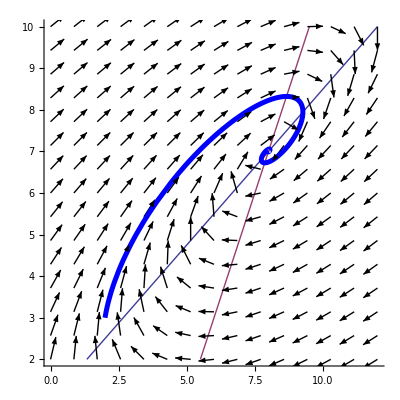

```mathematica
Show[p7,p8,p9]
```

```mathematica
Clear[A4,b4,ec4,eq4,var4,sol4,p7,p8,p9]
```

5.	ẋ=   x+3y-12	c.i. 	x(0)= 3
	ẏ=-3x+ y+ 6		y(0)= 2

```mathematica
A5={{1,3},{-3,1}};MatrixForm[A5](* Matriz A de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(1 | 3
-3 | 1)

```mathematica
b5={{-12},{6}};MatrixForm[b5](* Vector b de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(-12
6)

```mathematica
MatrixForm[LinearSolve[-A5,b5]](* Esto equivale a ({{Subscript[x, 1]^-}, {(x^-)_2}})=-A^-1b *)
```

(3
3)

b) Análisis de estabilidad

```mathematica
traA5=Tr[A5](*Traza de la matriz A*)
```

2

```mathematica
detA5=Det[A5](*Determinante de la matriz A*)
```

10

```mathematica
(traA5)^2-4detA5(* (TrazaA)^2-4det|A| *)
```

-36

```mathematica
ec5=CharacteristicPolynomial[A5,λ] (* Polinomio caracteristico de la matriz A *)
```

10-2 λ+λ^2

```mathematica
Solve[ec5==0,λ](* Obteniendo los valores propios *)
```

{{λ→1-3 ⅈ},{λ→1+3 ⅈ}}

c) Diagrama de fases

```mathematica
eq5={x'[t]==x[t]+3y[t]-12,y'[t]==-3x[t]+y[t]+6,x[0]==3,y[0]==2};
```

```mathematica
var5={x[t],y[t]};
```

```mathematica
sol5=DSolve[eq5,var5,t];
```

```mathematica
p10=ContourPlot[{x+3y-12==0,-3x+y+6==0},{x,0,6},{y,0,6},Axes->True,Frame->False];
```

```mathematica
p11=VectorFieldPlot[{x+3y-12,-3x+y+6},{x,0,6},{y,0,6},ScaleFunction->(1 &),AspectRatio->1];
```

```mathematica
p12=ParametricPlot[Evaluate[var5/.sol5],{t,0,7},PlotStyle->{Thickness[0.009],RGBColor[0,0,1]}];
```

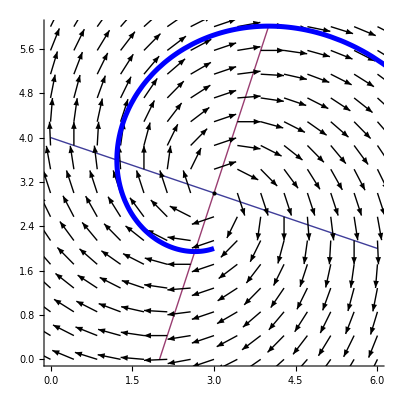

```mathematica
Show[p10,p11,p12]
```

```mathematica
Clear[A5,b5,ec5,eq5,var5,sol5,p10,p11,p12]
```

6.	ẋ=    x+3y-7	c.i. 	x(0)= 2
	ẏ= -6x - y+8		y(0)= 2

```mathematica
A6={{1,3},{-6,-1}};MatrixForm[A6](* Matriz A de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(1 | 3
-6 | -1)

```mathematica
b6={{-7},{8}};MatrixForm[b6](* Vector b de coeficientes constantes del sistema de ecuaciones diferenciales *)
```

(-7
8)

```mathematica
MatrixForm[LinearSolve[-A6,b6]](* Esto equivale a ({{Subscript[x, 1]^-}, {(x^-)_2}})=-A^-1b *)
```

(1
2)

b) Análisis de estabilidad

```mathematica
traA6=Tr[A6](*Traza de la matriz A*)
```

0

```mathematica
detA6=Det[A6](*Determinante de la matriz A*)
```

17

```mathematica
(traA6)^2-4detA6(* (TrazaA)^2-4det|A| *)
```

-68

```mathematica
ec6=CharacteristicPolynomial[A6,λ] (* Polinomio caracteristico de la matriz A *)
```

17+λ^2

```mathematica
Solve[ec6==0,λ](* Obteniendo los valores propios *)
```

{{λ→-ⅈ √17},{λ→ⅈ √17}}

c) Diagrama de fases

```mathematica
eq6={x'[t]==x[t]+3y[t]-7,y'[t]==-6x[t]-y[t]+8,x[0]==2,y[0]==2};
```

```mathematica
var6={x[t],y[t]};
```

```mathematica
sol6=DSolve[eq6,var6,t];
```

```mathematica
p13=ContourPlot[{x+3y-7==0,-6x-y+8==0},{x,-0.5,2.5},{y,0,4},Axes->True,Frame->False];
```

```mathematica
p14=VectorFieldPlot[{x+3y-7,-6x-y+8},{x,-0.5,2.5},{y,0,4},ScaleFunction->(1 &),AspectRatio->1];
```

```mathematica
p15=ParametricPlot[Evaluate[var6/.sol6],{t,0,5},PlotStyle->{Thickness[0.009],RGBColor[0,0,1]}];
```

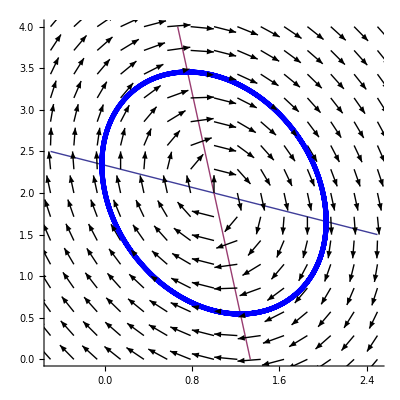

```mathematica
Show[p13,p14,p15]
```

```mathematica
Clear[A6,b6,ec6,eq6,var6,sol6,p13,p14,p15]
```